## Density Function

All lengths scales are given in units of ξ (i.e. the size of a vortex)

```mathematica
ρs[r_,l_,R_] = (r/R)^(2l) Exp[-(r/R)^2];
pρs[ρ_,z_,l_,R_] = ρs[Sqrt[ρ^2+z^2],l,R];
```

## Vortex Number Density

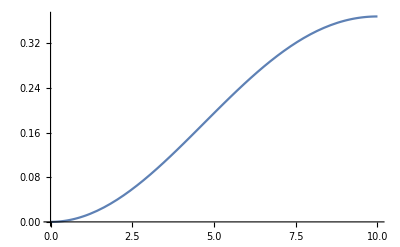

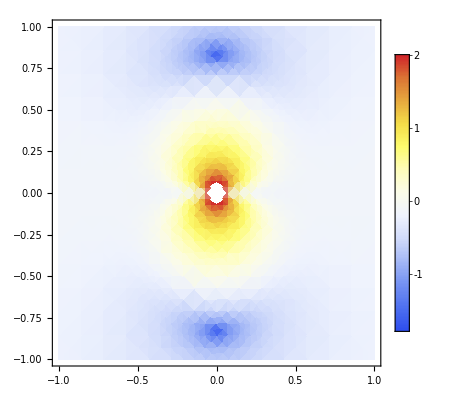

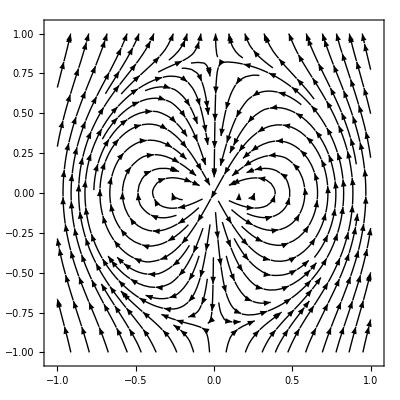

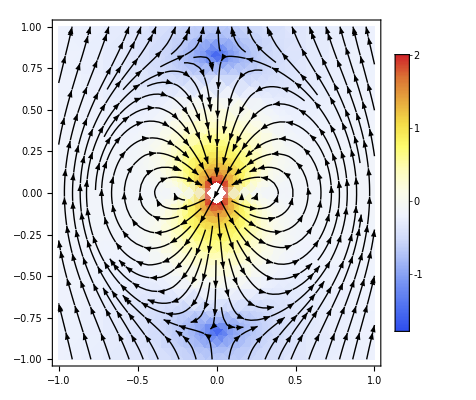

```mathematica
ω=0.7;
c =1/ω(Log[1/ω]+2ω-2);
nvr[ρ_,z_,l_,R_] = -c/2 Simplify[D[D[Log[pρs[ρ,z,l,R]],ρ],z]];
nvz[ρ_,z_,l_,R_]=1+c/2Simplify[1/ρ D[ρ D[Log[pρs[ρ,z,l,R]],ρ],ρ]];
amp[ρ_,z_,l_,R_]=Sqrt[nvr[ρ,z,l,R]^2+nvz[ρ,z,l,R]^2];

lt=1;
Rt=10;
MaxRad =Sqrt[lt];
Plot[ρs[r,lt,Rt],{r,0,MaxRad Rt},PlotRange->{0,All}]
dp=DensityPlot[Log10[ω amp[ρ,z,lt,Rt]],{ρ,-MaxRad,MaxRad},{z,-MaxRad,MaxRad},PlotLegends->Automatic,PlotRange->{-2,2},ColorFunction->"TemperatureMap"]
sp=StreamPlot[{nvr[ρ,z,lt,Rt],nvz[ρ,z,lt,Rt]},{ρ,-MaxRad,MaxRad},{z,-MaxRad,MaxRad},StreamPoints->100,StreamStyle->Black]
Show[dp,sp]
```

## Checking Assumptions

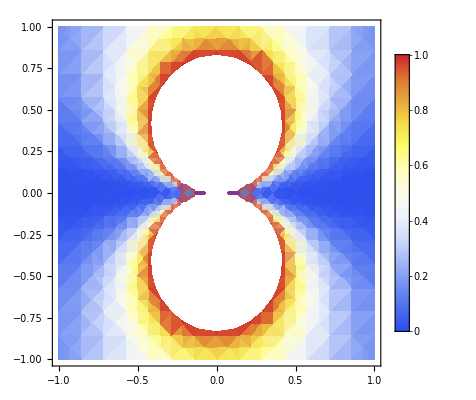

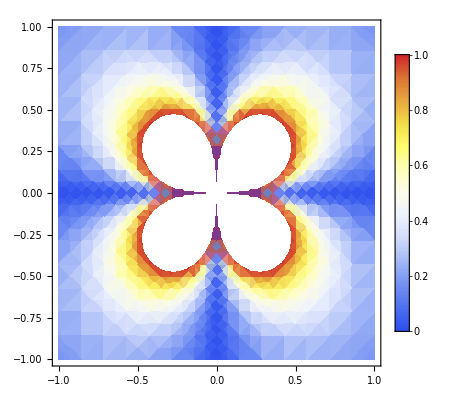

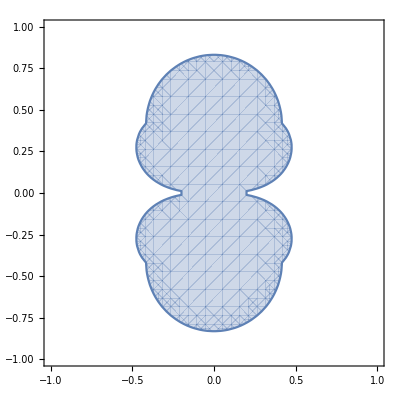

```mathematica
DensityPlot[Abs[nvz[ρ,z,lt,Rt]-1],{ρ,-MaxRad,MaxRad},{z,-MaxRad,MaxRad},PlotLegends->Automatic,PlotRange->{0,1},ColorFunction->"TemperatureMap"]
DensityPlot[Abs[nvr[ρ,z,lt,Rt]],{ρ,-MaxRad,MaxRad},{z,-MaxRad,MaxRad},PlotLegends->Automatic,PlotRange->{0,1},ColorFunction->"TemperatureMap"]
RegionPlot[{Abs[nvz[ρ,z,lt,Rt]-1]>1 || Abs[nvr[ρ,z,lt,Rt]]>1 || ω amp[ρ,z,lt,Rt]>1},{ρ,-MaxRad,MaxRad},{z,-MaxRad,MaxRad}]
```